```mathematica
k1f[s_]:=(s-π)HeavisideTheta[π-s]+(s-2π)*HeavisideTheta[2π-s]+(3π-s)*HeavisideTheta[3π-s]+(4π-s)*HeavisideTheta[4π-s]+(s-4π)HeavisideTheta[5π-s];
k2f[s_]:=(π-s)HeavisideTheta[π-s]+(s-2π)HeavisideTheta[2π-s]+(s-3π)HeavisideTheta[3π-s]+(8π-2s)HeavisideTheta[4π-s]+(s-4π)HeavisideTheta[5π-s];
```

```mathematica
H[t1_,t2_,δ_,k1_,k2_]:={{0,t1,0,0,0,ⅇ^(ⅈ k2) t1,0,t2},{t1,0,t2,0,ⅇ^(ⅈ k2) t1,0,0,0},{0,t2,0,t1,0,0,0,ⅇ^(ⅈ k1) t1},{0,0,t1,0,t2,0,ⅇ^(ⅈ k1) t1,0},{0,ⅇ^(-ⅈ k2) t1,0,t2,0,t1,0,0},{ⅇ^(-ⅈ k2) t1,0,0,0,t1,0,t2,0},{0,0,0,ⅇ^(-ⅈ k1) t1,0,t2,0,t1},{t2,0,ⅇ^(-ⅈ k1) t1,0,0,0,t1,0}}
```

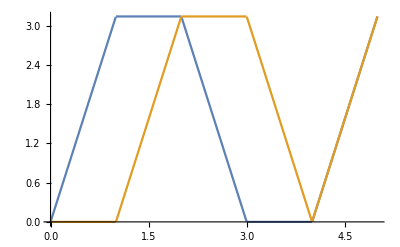

```mathematica
Plot[{k1f[s π],k2f[π s]},{s,0,5}]
```

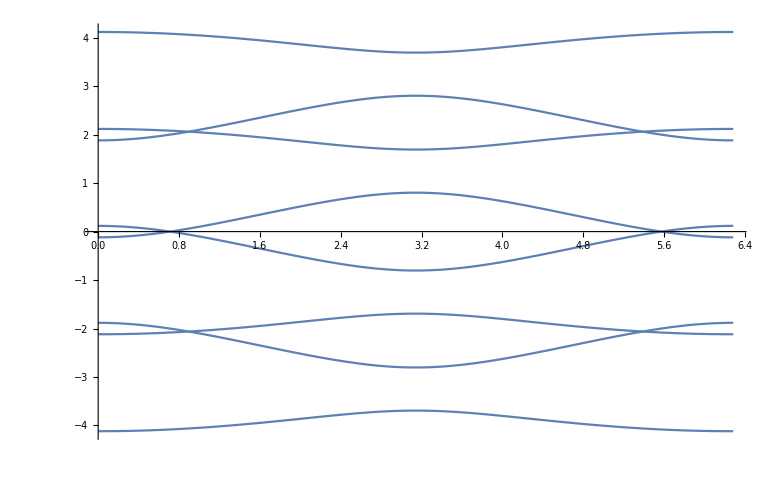

```mathematica
signconfig1 =  {-1,-1,-1,1,1,1,1,-1};With[{t1=1.0,t2=2.0,δ1=0.5},Plot[Sort[Eigenvalues[N[H[t1,t2,δ1,0,k]+DiagonalMatrix[δ1*signconfig1]]]],{k,0,2 π}]]
```

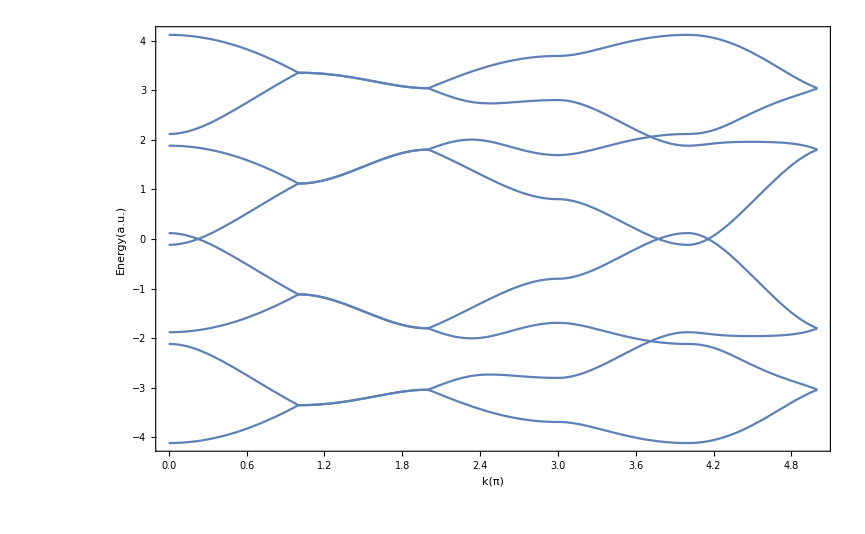

```mathematica
signconfig1 =  {-1,-1,-1,1,1,1,1,-1};With[{t1=1.0,t2=2.0,δ1=0.5},Plot[Sort[Eigenvalues[N[H[t1,t2,δ1,k1f[s*π],k2f[s*π]]+DiagonalMatrix[δ1*signconfig1]]]],{s,0,5},Frame->True,FrameLabel->{"k(π)","Energy(a.u.)"}]]
```